# SIRS

by   R. Adenane, F. Avram and AD.Halanay

## CRN for SIRS-FA:

```mathematica
(*Latex dictionary*)
Format[γr]:=Subscript[γ,r];Format[μi]:=Subscript[μ,i];Format[μs]:=Subscript[μ,s];Format[μr]:=Subscript[μ,r];
Format[γs]:=Subscript[γ,s];Format[γi]:=Subscript[γ,i];
(*SystemOpen@FileNameJoin[{$UserBaseDirectory, "FrontEnd"}]*)
ClearAll["Global‘*",s,i,r]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];AppendTo[$Path,"C:\\Users\\flori\\Dropbox\\EpidCRNmodels"];<<EpidCRN`;
(*input model using ReactionKinetics structure*)
(* Needs["ReactionKinetics`"];*)
(*Summary  of some key formulas, to ve rederived later*)
sd=(λ (γr+μr))/(γs μr+(γr+μr) μs);mR=β/(μi+γi);
(*particular cases and reparametrization conditions*)
cmu={μr->μ,μs->μ,λ->μ};
cbe=β->R(μi+γi);cR=R->R0/sd;
(*inputs*)
RN={0->"S","S"+"I"->2 "I","I"->"R","R"->"S","S"->"R","S"->0,"I"->0,"R"->0};
{spe, al, be, ga, Rv, RH, def} =extMat[RN];(*var=ToExpression[spe];*)
var={s,i,r};
par={λ,β,γi, γr,γs, μs, μi,μr};
cp=Thread[par>0];cv=Thread[var>=0];ct=Append[Join[cp,cv],R>0];

(*Universal notebook starts*)

RND=ReactionsData[RN];
Γ= RND["γ"]//Normal;

{comp,reac,nR,spec,nS,vol,vars,defi}=RND["complexes","reactionsteps","R","species","M","volpertgraph",
"variables","deficiency"];
Print["Stoichio mat Γ=",Γ//MatrixForm, " has rank ",MatrixRank[Γ]," and deficiency ", RND["deficiency"]," constants
are ",par]

Print[RND["variables"]//Length," variables=",RND["variables"],"=",var]
expo= RND["α"]//Normal;expo//MatrixForm
prod= RND["β"]//Normal;
rv=expM[var,(expo//Transpose)];
Rv=par*rv;RHS=Γ.Rv;
RHS={-i s β+r γr-s γs+λ-s μs,i s β-i γi-i μi,i γi-r γr+s γs-r μr};
jac=Grad[RHS,var];
so=Solve[Thread[RHS==0],var]//FullSimplify;
Print["RHS is ",RHS,"=",RHS//MatrixForm," fixed pts are"]
so//FullSimplify
(*check positivity of endemic solution*)inf={2};vx=var[[inf]];inp={1};vy=var[[inp]];vNy=Complement[var,vy];
Print["endemic pt pos when ",cvNy=FullSimplify[Reduce[Thread[(vNy/.so[[1]]/.cbe)>0]],ct],
" and R>1  starting from"]
Rc=cvNy[[1]]/λ;FullSimplify[Reduce[Rc>1],ct]
Print["Check: when mus=mur=mu, this becomes R0>1 or R>1/sd="]
Rc/.cmu//Simplify
(*Stability of DFE, using NGM script *)
mod={RHS,var,par};
jacI=Grad[RHS[[inf]],var[[inf]]]; 
ng=NGM[mod,inf];K=ng[[6]];M=ng[[1]];
Tm=ng[[5]];
F=ng[[4]];
Print["M is",M//MatrixForm, " and K=",K//MatrixForm," has eig",eig=K//Eigenvalues]
Print["R0=",R0=eig[[1]]]
minSiph[ToString/@{S,I,R},asoRea[RN]]
```

Stoichio mat Γ=(1 | -1 | 0 | 1 | -1 | -1 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | -1 | 1 | 0 | 0 | -1) has rank 3 and deficiency δ=N-L-S=6-2-3=1 constants
are {λ,β,γ_i,γ_r,γ_s,μ_s,μ_i,μ_r}

3 variables={c_S,c_I,c_R}={s,i,r}

(0 | 1 | 0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1)

RHS is {-i s β+r γ_r-s γ_s+λ-s μ_s,i s β-i γ_i-i μ_i,i γ_i-r γ_r+s γ_s-r μ_r}=(-i s β+r γ_r-s γ_s+λ-s μ_s
i s β-i γ_i-i μ_i
i γ_i-r γ_r+s γ_s-r μ_r) fixed pts are

{{s→(γ_i+μ_i)/β,i→(β λ (γ_r+μ_r)-(γ_i+μ_i) (γ_s μ_r+(γ_r+μ_r) μ_s))/(β γ_r μ_i+β (γ_i+μ_i) μ_r),r→(β γ_i λ-(γ_i+μ_i) (-γ_s μ_i+γ_i μ_s))/(β γ_r μ_i+β (γ_i+μ_i) μ_r)},{s→(λ (γ_r+μ_r))/(γ_s μ_r+(γ_r+μ_r) μ_s),i→0,r→(γ_s λ)/(γ_s μ_r+(γ_r+μ_r) μ_s)}}

endemic pt pos when (γ_s μ_r)/(γ_r+μ_r)+μ_s<R λ and R>1  starting from

γ_s μ_r>(γ_r+μ_r) (λ-μ_s)

Check: when mus=mur=mu, this becomes R0>1 or R>1/sd=

(γ_r+γ_s+μ)/(γ_r+μ)

Eigenvalues::matsq: Argument {{i β,0}} at position 1 is not a non-empty square matrix.

M is(s β-γ_i-μ_i) and K=(i β | 0) has eigEigenvalues[{{i β,0}}]

R0={{i β,0}}

{{I}}

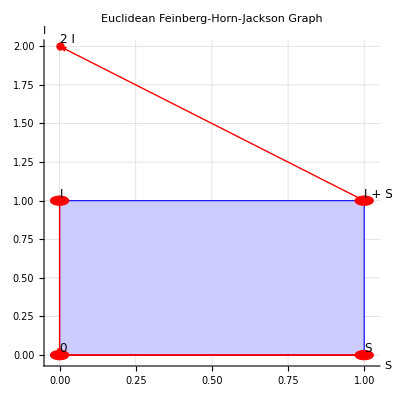

euS.pdf

```mathematica
(*SI model *)
RN={0->"S","S"+"I"->2 "I","S"->0,"I"->0};
{al,be,ga}=Take[stoichiometricMatrices[RN],3];
euSIR=EucFHJ[RN]
Export["euS.pdf",euSIR]
```